```mathematica
大粘滞系数下的位移统计性
```

-0.381623+0.175302 t

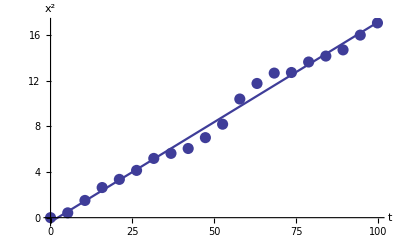

```mathematica
dis=NormalDistribution[0,1];
n=100;m=1000;δt=0.1;time=(m-1)*δt;α=0.5;
fr=Table[RandomReal[dis] √α,{i,n},{j,m}];
fr=Table[{δt*(i-1),fr[[j,i]]},{j,n},{i,m}];
fr=Table[Interpolation[fr[[i]]],{i,n}];
equs=
Table[{x''[t]+α*x'[t]==fr[[i]][t],x[0]==0,
x'[0]==0},{i,n}];
s=Table[NDSolve[equs[[i]],x,{t,0,time},
MaxSteps->∞],{i,n}];
s=Flatten[s];
sample=20;δt=time/(sample-1);result={};
Do[section=Table[x[δt*(i-1)]/.s[[j]],{j,n}];
AppendTo[result,
{δt*(i-1),Sum[section[[j]]^2,{j,n}]/n}],
{i,sample}]
fit=Fit[result,{1,t},t]
g1=Plot[fit,{t,0,time},
PlotStyle->Thickness[0.004]];
g2=ListPlot[result,PlotStyle->PointSize[0.02]];
Show[{g1,g2},AxesStyle->Thickness[0.003],
AxesLabel->{"t","x^2"},BaseStyle->{FontSize->13}]
Clear[dis,α,equs,fr,s,result,x,fit,g1,g2]
```